# Работа над примером из статьи

```mathematica
adj={
{∞, 200 , ∞, ∞, ∞, ∞,12y,∞},
{∞, ∞, 2y,∞,10, ∞,∞,50},
{∞,∞,∞,2y,∞,∞,∞,10},
{∞,∞,∞,∞,40,∞,∞,∞},
{∞,10,∞,∞,∞,12y,∞,∞},
{∞,∞,∞,∞,12y,∞,210,∞},
{12y,∞,∞,∞,∞,210,∞,∞},
{∞, ∞,10,∞,∞,∞,∞,∞}
};
```

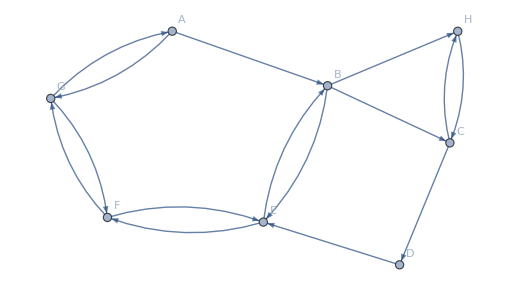

```mathematica
graph = WeightedAdjacencyGraph[adj, VertexLabels->Table[i->Capitalize@Alphabet[][[i]],{i,8}]]
```

```mathematica
MatrixForm[adj, TableHeadings->{Table[Capitalize@Alphabet[][[i]],{i,8}],Table[Capitalize@Alphabet[][[i]],{i,8}]}]
```

( | A | B | C | D | E | F | G | H
A | ∞ | 200 | ∞ | ∞ | ∞ | ∞ | 12 y | ∞
B | ∞ | ∞ | 2 y | ∞ | 10 | ∞ | ∞ | 50
C | ∞ | ∞ | ∞ | 2 y | ∞ | ∞ | ∞ | 10
D | ∞ | ∞ | ∞ | ∞ | 40 | ∞ | ∞ | ∞
E | ∞ | 10 | ∞ | ∞ | ∞ | 12 y | ∞ | ∞
F | ∞ | ∞ | ∞ | ∞ | 12 y | ∞ | 210 | ∞
G | 12 y | ∞ | ∞ | ∞ | ∞ | 210 | ∞ | ∞
H | ∞ | ∞ | 10 | ∞ | ∞ | ∞ | ∞ | ∞)

### Все пути A-H, A-F, G-D

```mathematica
getPaths[graph_,from_, to_]:=MovingMap[DirectedEdge@@#&, #,1]& /@FindPath[graph, from, to,∞, All]
```

```mathematica
AF = getPaths[graph, 1,6];
Subscript[ξ, 1] = 20;
GD = getPaths[graph, 7,4];
Subscript[ξ, 2] = 100;
AH = getPaths[graph, 1,8]; 
Subscript[ξ, 3] = 10;
```

```mathematica
edges = {1->2,2->3,3->4,4->5,1->7,7->1,7->6,6->7,5->6,6->5,2->5,5->2,2->8,8->3,3->8};
```

### Построим матрицу С

```mathematica
getC[paths_ , edges_]:=Table[Table[MemberQ[paths[[j]], edges[[i]]],{j, Length@paths}], {i,Length@edges }]/.{True->1, False->0}
```

```mathematica
c = getC[AF~Join~GD~Join~AH, EdgeList@graph];
MatrixForm@c
```

(0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1
0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

### Создадим вектор потока и вычислим

```mathematica
X = Table[Subscript[x, i], {i, Total[Length/@{AF, GD, AH}]}]ᵀ;
```

```mathematica
flows = c.X;  (*потоки по дугам*)
MatrixForm@flows
```

(x_2+x_3+x_4+x_5+x_7+x_9+x_10
x_1+x_11+x_12
x_3+x_5+x_6+x_10+x_12
x_2
x_4+x_7+x_8+x_9+x_11
x_3+x_4+x_5+x_6+x_7+x_8
x_10+x_12
x_3+x_4
x_6+x_8+x_11+x_12
x_2+x_3+x_4
x_6+x_8+x_11+x_12
0
x_5+x_7
x_1+x_6+x_8+x_11+x_12
x_4+x_7+x_8)

```mathematica
Subscript[f, α]=MapIndexed[Integrate[#1[[1]],y]/.{y->flows[[First@#2]]}&,Flatten[MapIndexed[{#1,DirectedEdge@@#2}&,adj, {2}]/.{∞,__}->Nothing,1]];

MatrixForm[Subscript[f, α]]
```

(200 (x_2+x_3+x_4+x_5+x_7+x_9+x_10)
6 (x_1+x_11+x_12)^2
(x_3+x_5+x_6+x_10+x_12)^2
10 x_2
50 (x_4+x_7+x_8+x_9+x_11)
(x_3+x_4+x_5+x_6+x_7+x_8)^2
10 (x_10+x_12)
40 (x_3+x_4)
10 (x_6+x_8+x_11+x_12)
6 (x_2+x_3+x_4)^2
6 (x_6+x_8+x_11+x_12)^2
0
6 (x_5+x_7)^2
210 (x_1+x_6+x_8+x_11+x_12)
10 (x_4+x_7+x_8))

### Решение экстремальной задачи

```mathematica
F =Plus@@Subscript[f, α];
opt = QuadraticOptimization[
F,
Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 3]+Subscript[x, 4]==20 &&Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 7]+Subscript[x, 8]==100&& Subscript[x, 9]+Subscript[x, 10]+Subscript[x, 11]+Subscript[x, 12]== 10&& Apply[And,#>=0&/@{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10],Subscript[x, 11],Subscript[x, 12]}],
{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10],Subscript[x, 11],Subscript[x, 12]}
];
MatrixForm[opt]
```

(x_1→10.
x_2→10.
x_3→0.
x_4→0.
x_5→14.8647
x_6→15.1353
x_7→35.9686
x_8→34.0314
x_9→10.
x_10→9.08108×10^-11
x_11→0.
x_12→0.)

```mathematica
MatrixForm[flows.c]
```

(2 x_1+x_6+x_8+2 x_11+2 x_12
3 x_2+2 x_3+2 x_4+x_5+x_7+x_9+x_10
2 x_2+5 x_3+4 x_4+3 x_5+2 x_6+2 x_7+x_8+x_9+2 x_10+x_12
2 x_2+4 x_3+6 x_4+2 x_5+x_6+4 x_7+3 x_8+2 x_9+x_10+x_11
x_2+3 x_3+2 x_4+4 x_5+2 x_6+3 x_7+x_8+x_9+2 x_10+x_12
x_1+2 x_3+x_4+2 x_5+5 x_6+x_7+4 x_8+x_10+3 x_11+4 x_12
x_2+2 x_3+4 x_4+3 x_5+x_6+5 x_7+3 x_8+2 x_9+x_10+x_11
x_1+x_3+3 x_4+x_5+4 x_6+3 x_7+6 x_8+x_9+4 x_11+3 x_12
x_2+x_3+2 x_4+x_5+2 x_7+x_8+2 x_9+x_10+x_11
x_2+2 x_3+x_4+2 x_5+x_6+x_7+x_9+3 x_10+2 x_12
2 x_1+x_4+3 x_6+x_7+4 x_8+x_9+5 x_11+4 x_12
2 x_1+x_3+x_5+4 x_6+3 x_8+2 x_10+4 x_11+6 x_12)

```mathematica
Dimensions[adj]
```

{8,8}

```mathematica
flows/.opt
```

{70.8333,10.,30.,10.,80.,100.,9.08108×10^-11,0.,49.1667,10.,49.1667,0,50.8333,59.1667,70.}

```mathematica
t = First[Flatten[MapIndexed[{#1,DirectedEdge@@#2}&,adj, {2}]/.{∞,__}->Nothing,1]ᵀ];
```

```mathematica
tᵀ.c
```

{210+12 y,210+12 y,240+16 y,300+14 y,200+16 y,220+16 y,260+14 y,280+14 y,250,210+2 y,270+24 y,230+26 y}

```mathematica
Length@t
```

15

```mathematica
MapIndexed[t[[First@#2]]/.y->#1&, flows/.opt]
```

{200,120.,60.,10,50,200.,10,40,10,120.,590.,210,610.,210,10}

```mathematica
MapIndexed[t[[First@#2]]/.y->#1&, flows/.opt]ᵀ.c
```

{330.,330.,620.,620.,1070.,1070.,1070.,1070.,250.,270.,980.,1000.}

# Реализация курсовой

### Вспомогательные функции

```mathematica
ClearAll[getC]
getC[paths_ , edges_]:=Table[Table[MemberQ[paths[[j]], edges[[i]]],{j, Length@paths}], {i,Length@edges }]/.{True->1, False->0}
```

```mathematica
ClearAll[getTimeInt]
getTimeInt[adj_?MatrixQ, flows_]:=MapIndexed[Integrate[#1[[1]],y]/.{y->flows[[First@#2]]}&,Flatten[MapIndexed[{#1,DirectedEdge@@#2}&,adj, {2}]/.{∞,__}->Nothing,1]];
```

```mathematica
ClearAll[getStreamVector]
getStreamVector[paths_List]:= Table[Subscript[x, i], {i, Total[Length/@paths]}]ᵀ;
```

```mathematica
ClearAll[getRegs]
getRegs[vars_List, lims_List, paths_List]:=MapIndexed[Plus@@#1 == lims[[First@#2]]&,TakeList[vars, Length/@paths]]
```

```mathematica
ClearAll[getPaths]
getPaths[graph_,{from_, to_}]:=MovingMap[DirectedEdge@@#&, #,1]& /@FindPath[graph, from, to,∞, All]
```

```mathematica
ClearAll[getTime]
getTime[adj_]:=First[Flatten[MapIndexed[{#1,DirectedEdge@@#2}&,adj, {2}]/.{∞,__}->Nothing,1]ᵀ]
```

```mathematica
ClearAll[travelTime]
travelTime[time_, cost_, c_]:=MapIndexed[time[[First@#2]]/.y->#1&, cost]ᵀ.c
```

### Решение экстремальной задачи

#### Вспомогательные функции

```mathematica
ClearAll[joinColumns]
joinColumns[Q_, A_]:=Join[Qᵀ,-A]ᵀ
```

```mathematica
ClearAll[checkSolution]
checkSolution[solve_, cutted_, vars_]:=If[AllTrue[cutted, #>=0&], solve[[;;Length@vars]], -1]
```

```mathematica
ClearAll[solveSystem]
solveSystem[Q_,b_, i_, A_, M2_, vars_ ]:=Module[
{
solve
},
Print[{MatrixForm@i, MatrixForm[Join[joinColumns[Q, A[[M2~Join~i]]],#~Join~Table[0, Length@i]&/@(A[[i]])]], MatrixForm@b}];
solve = Quiet@Check[LinearSolve[Join[joinColumns[Q, A[[M2~Join~i]]],#~Join~Table[0, Length@i]&/@(A[[i]])], b],-1];

If[ListQ@solve,
Print[Solve];
checkSolution[solve, Delete[solve[[1;;Length@vars]], {#}&/@i]~Join~solve[[Length@vars+1;;]][[Length@M2+1;;]], vars],
-1]
]
```

```mathematica
ClearAll[generateA]
generateA[vars_, regs_]:=Join[#, Table[0, Length@regs]]&/@Join[DiagonalMatrix[Table[1, Length@vars]], Normal[Last@CoefficientArrays[#, vars]&/@regs]]
```

#### Основные функции

```mathematica
ClearAll[getOptimumByWolfram] (*Решение через встроенную функцию QuadraticOptimization*)
getOptimumByWolfram[f_, regs_, vars_List]:= QuadraticOptimization[Plus@@f,Apply[And,regs]&& Apply[And,#>=0&/@vars],vars];
```

```mathematica
ClearAll[myGetOptimum] (*Мое решение через критерий оптимальности в форме Куна-Таккера*)
myGetOptimum[f_, regs_, vars_List]:= Module[
{
Q=CoefficientArrays[Join[#==0&/@Expand/@Grad[f, vars],regs], vars] //Normal,
M2 = Table[Length@vars+i, {i, Length@regs}],
M1= Table[i, {i, Length@vars}],
A=generateA[vars, regs],
i,b
},

{b, Q} = Q;
b = b/._?BooleanQ->0;

i= Subsets[M1];
Print[MatrixForm/@i];
(solveSystem[Q,-b~Join~Table[0, Length@#], #, A, M2, vars]&/@i)
(*{MatrixForm@(-b), MatrixForm@Q, MatrixForm@A}*)
]
```

#### Оптимизация функции из статьи 1

```mathematica
f = 10 Subscript[x, 2]+40 (Subscript[x, 3]+Subscript[x, 4])+6 (Subscript[x, 2]+Subscript[x, 3]+Subscript[x, 4])^2+6 (Subscript[x, 5]+Subscript[x, 7])^2+10 (Subscript[x, 4]+Subscript[x, 7]+Subscript[x, 8])+(Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 7]+Subscript[x, 8])^2+200 (Subscript[x, 2]+Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 7]+Subscript[x, 9]+Subscript[x, 10])+50 (Subscript[x, 4]+Subscript[x, 7]+Subscript[x, 8]+Subscript[x, 9]+Subscript[x, 11])+10 (Subscript[x, 10]+Subscript[x, 12])+(Subscript[x, 3]+Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 10]+Subscript[x, 12])^2+6 (Subscript[x, 1]+Subscript[x, 11]+Subscript[x, 12])^2+10 (Subscript[x, 6]+Subscript[x, 8]+Subscript[x, 11]+Subscript[x, 12])+6 (Subscript[x, 6]+Subscript[x, 8]+Subscript[x, 11]+Subscript[x, 12])^2+210 (Subscript[x, 1]+Subscript[x, 6]+Subscript[x, 8]+Subscript[x, 11]+Subscript[x, 12]);
vars={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7],Subscript[x, 8],Subscript[x, 9],Subscript[x, 10],Subscript[x, 11],Subscript[x, 12]};
regs = {Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 3]+Subscript[x, 4]==20,Subscript[x, 5]+Subscript[x, 6]+Subscript[x, 7]+Subscript[x, 8]==100,Subscript[x, 9]+Subscript[x, 10]+Subscript[x, 11]+Subscript[x, 12]==10};
```

```mathematica
myGetOptimum[f, regs, vars]
```

(12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 12 | 12
0 | 12 | 12 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 12 | 16 | 14 | 4 | 4 | 2 | 2 | 0 | 2 | 0 | 2
0 | 12 | 14 | 14 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 0
0 | 0 | 4 | 2 | 16 | 4 | 14 | 2 | 0 | 2 | 0 | 2
0 | 0 | 4 | 2 | 4 | 16 | 2 | 14 | 0 | 2 | 12 | 14
0 | 0 | 2 | 2 | 14 | 2 | 14 | 2 | 0 | 0 | 0 | 0
0 | 0 | 2 | 2 | 2 | 14 | 2 | 14 | 0 | 0 | 12 | 12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2
12 | 0 | 0 | 0 | 0 | 12 | 0 | 12 | 0 | 0 | 24 | 24
12 | 0 | 2 | 0 | 2 | 14 | 0 | 12 | 0 | 2 | 24 | 26
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

```mathematica
MatrixForm@Grad[x^2-2x*y+3 y^2,{x,y}]
```

(2 x-2 y
-2 x+6 y)

```mathematica
{b, q}=CoefficientArrays[Join[#==0&/@Expand/@Grad[x^2-2x*y+3 y^2, {x,y}],{-x+y==-1}]]//Normal;
```

```mathematica
q = {{2,-2, 1},{-2,6, -1},{-1,1, 0}};
```

```mathematica
LinearSolve[q, -b]
```

{1,0,-2}

#### Оптимизация функции из статьи 2

```mathematica
f =81 Subscript[x, 1]+Subscript[x, 1]^2/2+57 Subscript[x, 2]+Subscript[x, 2]^2/2+13 Subscript[x, 3]+Subscript[x, 3]^2/2+3 (Subscript[x, 1]+Subscript[x, 3])^2+5/2 (Subscript[x, 2]+Subscript[x, 3])^2;
vars={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]};
regs = {Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 3]==12};
```

```mathematica
myGetOptimum[f, regs, vars]
```

(7 | 0 | 6
0 | 6 | 5
6 | 5 | 12
1 | 1 | 1)

{{},(7 | 0 | 6 | -1
0 | 6 | 5 | -1
6 | 5 | 12 | -1
1 | 1 | 1 | 0),(-81
-57
-13
12)}

{-8/55,276/55,392/55,6751/55}

{(1),(7 | 0 | 6 | -1 | -1
0 | 6 | 5 | -1 | 0
6 | 5 | 12 | -1 | 0
1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0),(-81
-57
-13
12
0)}

{0,5,7,122,1}

{(2),(7 | 0 | 6 | -1 | 0
0 | 6 | 5 | -1 | -1
6 | 5 | 12 | -1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0),(-81
-57
-13
12
0)}

{4/7,0,80/7,1075/7,-276/7}

{(3),(7 | 0 | 6 | -1 | 0
0 | 6 | 5 | -1 | 0
6 | 5 | 12 | -1 | -1
1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0),(-81
-57
-13
12
0)}

{48/13,108/13,0,1389/13,-392/13}

{(1
2),(7 | 0 | 6 | -1 | -1 | 0
0 | 6 | 5 | -1 | 0 | -1
6 | 5 | 12 | -1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0),(-81
-57
-13
12
0
0)}

{0,0,12,157,-4,-40}

{(1
3),(7 | 0 | 6 | -1 | -1 | 0
0 | 6 | 5 | -1 | 0 | 0
6 | 5 | 12 | -1 | 0 | -1
1 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0),(-81
-57
-13
12
0
0)}

{0,12,0,129,-48,-56}

{(2
3),(7 | 0 | 6 | -1 | 0 | 0
0 | 6 | 5 | -1 | -1 | 0
6 | 5 | 12 | -1 | 0 | -1
1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0),(-81
-57
-13
12
0
0)}

{12,0,0,165,-108,-80}

{(1
2
3),(7 | 0 | 6 | -1 | -1 | 0 | 0
0 | 6 | 5 | -1 | 0 | -1 | 0
6 | 5 | 12 | -1 | 0 | 0 | -1
1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0),(-81
-57
-13
12
0
0
0)}

-1

{{0,5,7}}

### Основная функция

```mathematica
ClearAll[vardrop]
vardrop[adj_?MatrixQ, lims_?ListQ, dirs_List]:=Module[
{
graph =  WeightedAdjacencyGraph[adj],
paths, regs, X, flow, opt
},
paths=Map[getPaths[graph, #]&, dirs];
X=getStreamVector[paths];
flow= getC[Join@@paths, EdgeList@graph].X;
opt=getOptimumByWolfram[getTimeInt[adj,flow], getRegs[X, lims, paths], X];

{travelTime[getTime[adj], flow/.opt, getC[Join@@paths, EdgeList@graph]], opt}
]
```

## Пример работы

### 1.

```mathematica
adj={
{∞, 200 , ∞, ∞, ∞, ∞,12y,∞},
{∞, ∞, 2y,∞,10, ∞,∞,50},
{∞,∞,∞,2y,∞,∞,∞,10},
{∞,∞,∞,∞,40,∞,∞,∞},
{∞,10,∞,∞,∞,12y,∞,∞},
{∞,∞,∞,∞,12y,∞,210,∞},
{12y,∞,∞,∞,∞,210,∞,∞},
{∞, ∞,10,∞,∞,∞,∞,∞}
};
MatrixForm[adj, TableHeadings->{Table[Capitalize@Alphabet[][[i]],{i,8}],Table[Capitalize@Alphabet[][[i]],{i,8}]}]
WeightedAdjacencyGraph[adj]
```

( | A | B | C | D | E | F | G | H
A | ∞ | 200 | ∞ | ∞ | ∞ | ∞ | 12 y | ∞
B | ∞ | ∞ | 2 y | ∞ | 10 | ∞ | ∞ | 50
C | ∞ | ∞ | ∞ | 2 y | ∞ | ∞ | ∞ | 10
D | ∞ | ∞ | ∞ | ∞ | 40 | ∞ | ∞ | ∞
E | ∞ | 10 | ∞ | ∞ | ∞ | 12 y | ∞ | ∞
F | ∞ | ∞ | ∞ | ∞ | 12 y | ∞ | 210 | ∞
G | 12 y | ∞ | ∞ | ∞ | ∞ | 210 | ∞ | ∞
H | ∞ | ∞ | 10 | ∞ | ∞ | ∞ | ∞ | ∞)

-Graphics-

```mathematica
getPaths[WeightedAdjacencyGraph[adj], {}]
```

```mathematica
MatrixForm/@vardrop[adj, {20, 100, 10}, {{1,6},{7,4},{1,8}}]
```

{(330.
330.
620.
620.
1070.
1070.
1070.
1070.
250.
270.
980.
1000.),(x_1→10.
x_2→10.
x_3→0.
x_4→0.
x_5→0
x_6→30
x_7→50.8333
x_8→19.1667
x_9→10.
x_10→0
x_11→0.
x_12→0.)}

{(330.
330.
620.
620.
1070.
1070.
1070.
1070.
250.
270.
980.
1000.),(x_1→10.
x_2→10.
x_3→0.
x_4→0.
x_5→14.8647
x_6→15.1353
x_7→35.9686
x_8→34.0314
x_9→10.
x_10→9.08108×10^-11
x_11→0.
x_12→0.)}

### 1. Добавили нулевой мост 7-5

```mathematica
adjNew={
{∞, 200 , ∞, ∞, ∞, ∞,12y,∞},
{∞, ∞, 2y,∞,10, ∞,∞,50},
{∞,∞,∞,2y,∞,∞,∞,10},
{∞,∞,∞,∞,40,∞,∞,∞},
{∞,10,∞,∞,∞,12y,∞,∞},
{∞,∞,∞,∞,12y,∞,210,∞},
{12y,∞,∞,∞,0,210,∞,∞},
{∞, ∞,10,∞,∞,∞,∞,∞}
};
MatrixForm[adjNew, TableHeadings->{Table[Capitalize@Alphabet[][[i]],{i,8}],Table[Capitalize@Alphabet[][[i]],{i,8}]}]
WeightedAdjacencyGraph[adjNew]
```

( | A | B | C | D | E | F | G | H
A | ∞ | 200 | ∞ | ∞ | ∞ | ∞ | 12 y | ∞
B | ∞ | ∞ | 2 y | ∞ | 10 | ∞ | ∞ | 50
C | ∞ | ∞ | ∞ | 2 y | ∞ | ∞ | ∞ | 10
D | ∞ | ∞ | ∞ | ∞ | 40 | ∞ | ∞ | ∞
E | ∞ | 10 | ∞ | ∞ | ∞ | 12 y | ∞ | ∞
F | ∞ | ∞ | ∞ | ∞ | 12 y | ∞ | 210 | ∞
G | 12 y | ∞ | ∞ | ∞ | 0 | 210 | ∞ | ∞
H | ∞ | ∞ | 10 | ∞ | ∞ | ∞ | ∞ | ∞)

-Graphics-

### 2.

( | A | B | C | D | E | F | G
A | ∞ | 200 | ∞ | ∞ | ∞ | ∞ | 12 y
B | ∞ | ∞ | 2 y | ∞ | 10 | ∞ | ∞
C | ∞ | ∞ | ∞ | 2 y | ∞ | ∞ | ∞
D | ∞ | ∞ | ∞ | ∞ | 40 | ∞ | ∞
E | ∞ | 10 | ∞ | ∞ | ∞ | 12 y | ∞
F | ∞ | ∞ | ∞ | ∞ | 12 y | ∞ | 210
G | 12 y | ∞ | ∞ | ∞ | ∞ | 210 | ∞)

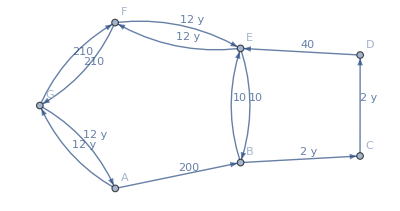

```mathematica
adj={
{∞, 200 , ∞, ∞, ∞, ∞,12y},
{∞, ∞, 2y,∞,10, ∞,∞},
{∞,∞,∞,2y,∞,∞,∞},
{∞,∞,∞,∞,40,∞,∞},
{∞,10,∞,∞,∞,12y,∞},
{∞,∞,∞,∞,12y,∞,210},
{12y,∞,∞,∞,∞,210,∞}

};
MatrixForm[adj, TableHeadings->{Table[Capitalize@Alphabet[][[i]],{i,7}],Table[Capitalize@Alphabet[][[i]],{i,7}]}]
WeightedAdjacencyGraph[adj, VertexLabels->Table[i->Capitalize@Alphabet[][[i]],{i,7}], EdgeLabels->Placed["EdgeWeight", {1/2,{0,0}}] ]
```

```mathematica
MatrixForm/@vardrop[adj, {30,50}, {{1,6},{7,4}}]
```

6 x_1^2+10 x_2+40 x_3+6 (x_2+x_3)^2+6 x_4^2+200 (x_2+x_3+x_4)+10 x_5+6 x_5^2+210 (x_1+x_5)+2 (x_3+x_4+x_5)^2

{(390.
390.
620.
710.
710.),(x_1→15.
x_2→15.
x_3→0.
x_4→25.8333
x_5→24.1667)}

```mathematica
getPaths[WeightedAdjacencyGraph[adj], {7,4}]
```

{{7->1,1->2,2->3,3->4},{7->6,6->5,5->2,2->3,3->4}}

### 2. Добавили нулевой мост E-G, G-E

( | A | B | C | D | E | F | G
A | ∞ | 200 | ∞ | ∞ | ∞ | ∞ | 12 y
B | ∞ | ∞ | 2 y | ∞ | 10 | ∞ | ∞
C | ∞ | ∞ | ∞ | 2 y | ∞ | ∞ | ∞
D | ∞ | ∞ | ∞ | ∞ | 40 | ∞ | ∞
E | ∞ | 10 | ∞ | ∞ | ∞ | 12 y | 0
F | ∞ | ∞ | ∞ | ∞ | 12 y | ∞ | 210
G | 12 y | ∞ | ∞ | ∞ | 0 | 210 | ∞)

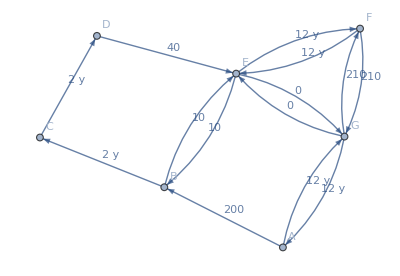

```mathematica
adj={
{∞, 200 , ∞, ∞, ∞, ∞,12y},
{∞, ∞, 2y,∞,10, ∞,∞},
{∞,∞,∞,2y,∞,∞,∞},
{∞,∞,∞,∞,40,∞,∞},
{∞,10,∞,∞,∞,12y,0},
{∞,∞,∞,∞,12y,∞,210},
{12y,∞,∞,∞,0,210,∞}

};
MatrixForm[adj, TableHeadings->{Table[Capitalize@Alphabet[][[i]],{i,7}],Table[Capitalize@Alphabet[][[i]],{i,7}]}]
g =WeightedAdjacencyGraph[adj, VertexLabels->Table[i->Capitalize@Alphabet[][[i]],{i,7}], EdgeLabels->Placed["EdgeWeight", {1/2,{0,0}}] ]
```

```mathematica
MatrixForm/@vardrop[adj, {30, 50}, {{1, 6}, {7,4}}]
```

(x_3+x_4+x_5+x_6+x_8
x_1+x_2
x_5+x_6+x_7+x_8+x_9
x_3+x_4
x_5+x_6+x_7+x_8+x_9
x_5+x_6
x_7+x_9
x_2+x_3+x_5
x_4+x_6
x_9
0
x_8
x_2+x_7
x_1+x_4+x_6+x_9)

(x_1+x_2+x_3+x_4+x_5+x_6==30
x_7+x_8+x_9==50)

{(420.
420.
420.
420.
650.
650.
210.
400.
420.),(x_1→7.2124
x_2→10.2876
x_3→7.2124
x_4→5.2876
x_5→0.
x_6→0.
x_7→50.
x_8→0.
x_9→0.)}

```mathematica
EdgeList@g
```

{1->2,1->7,2->3,2->5,3->4,4->5,5->2,5->6,6->5,6->7,7->1,7->6}

### 3. Пример с реальными дорогами

```mathematica
m = ({{0, 0, 0, 0, 54, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 122, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 37, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 37, 0, 0, 132, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 409, 0, 0, 0, 0, 0, 0}, {54, 0, 0, 0, 0, 2, 128, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 132, 2, 0, 0, 0, 0, 92, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 128, 0, 0, 0, 129, 0, 0, 0, 78, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 122, 0, 0, 0, 0, 0, 0, 33, 0, 0, 0, 0, 185, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 92, 0, 0, 0, 0, 0, 0, 0, 0, 0, 94, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 92, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 6, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 6, 0, 92, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 245, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 78, 0, 0, 0, 0, 92, 0, 0, 0, 0, 0, 0, 127, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 185, 0, 0, 0, 0, 0, 0, 39, 0, 0, 82, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 39, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 94, 0, 0, 0, 0, 0, 0, 0, 113, 0, 0, 49, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 113, 0, 97, 0, 0, 0, 0, 0, 0, 0, 0, 0, 225, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 82, 0, 0, 97, 0, 0, 0, 0, 0, 128, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 127, 0, 0, 0, 0, 0, 0, 52, 0, 0, 0, 0, 0, 0, 145, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 49, 0, 0, 52, 0, 0, 0, 0, 0, 0, 0, 0, 207, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 56, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 90, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 128, 0, 0, 0, 0, 0, 10, 0, 0, 0, 0, 0, 0, 0, 0, 0, 129, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 10, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 245, 0, 0, 0, 0, 0, 0, 0, 0, 0, 90, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 138, 0, 0, 0, 0, 86, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 145, 0, 0, 0, 0, 0, 0, 138, 0, 0, 0, 0, 0, 0, 88, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 225, 0, 0, 207, 56, 0, 0, 10, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 19, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 409, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 19, 0, 55, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 55, 0, 124, 0, 0, 0, 111}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 86, 0, 0, 0, 0, 124, 0, 148, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 88, 0, 0, 0, 0, 148, 0, 333, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 129, 0, 0, 0, 0, 0, 0, 0, 0, 0, 333, 0, 75, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 75, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 111, 0, 0, 0, 0, 0}});
m=Map[Map[If[#!=0,#/2. + Round[200./#, 0.01]*y,0]&, #]&, m];
m = ReplaceAll[m, 0->∞];
```

```mathematica
m[[1,7]] = 0;
```

```mathematica
g=-Graphics-;
```

```mathematica
EdgeList@WeightedAdjacencyGraph@m
```

{1->5,2->8,3->4,4->3,4->6,4->30,5->1,5->6,5->7,6->4,6->5,6->10,7->2,7->5,7->9,7->13,8->2,8->9,8->14,8->33,8->34,9->6,9->16,10->7,11->12,12->11,12->13,12->25,13->7,13->12,13->19,14->8,14->15,14->18,15->14,16->9,16->17,16->20,17->16,17->18,17->28,18->14,18->17,18->23,18->25,19->13,19->20,19->27,20->16,20->19,20->28,21->28,22->25,23->18,23->24,23->34,24->23,25->12,25->22,25->26,26->25,26->27,26->32,27->19,27->26,27->33,28->17,28->20,28->21,28->24,29->30,30->4,30->29,30->31,31->30,31->32,31->36,32->26,32->31,32->33,33->27,33->32,33->34,34->23,34->33,34->35,35->34,36->31}

```mathematica
getPaths[WeightedAdjacencyGraph@m, {1, 33}][[286]]
```

{1->5,5->7,7->2,2->8,8->14,14->18,18->17,17->28,28->20,20->16,16->9,9->6,6->4,4->30,30->31,31->32,32->26,26->25,25->12,12->13,13->19,19->27,27->33}

```mathematica
getPaths[WeightedAdjacencyGraph@m, {1, 33}][[11]]
```

{1->7,7->2,2->8,8->14,14->18,18->23,23->34,34->33}

```mathematica
{T, vars}=vardrop[m ,{40}, {{1, 33}}];
```

```mathematica
Min@T
Position[T, Min@T] 
Length@T
```

497.865

{{11}}

```mathematica
Max@T
Position[T, Max@T] 
Length@T
```

1625.33

{{286}}

293

```mathematica
GraphPlot@WeightedAdjacencyGraph@m
```

```mathematica
MatrixForm[ReplaceAll[Replace[Most@ArrayRules@UpperTriangularize@m,{x_,y_}:>UndirectedEdge[x,y],{2}], (UndirectedEdge[x_,y_]->∞) -> Nothing]]
```

(1<->5→27.+3.7 y
2<->8→61.+1.64 y
3<->4→18.5+5.41 y
4<->6→66.+1.52 y
4<->30→204.5+0.49 y
5<->6→1.+100. y
5<->7→64.+1.56 y
6<->10→46.+2.17 y
7<->9→64.5+1.55 y
7<->13→39.+2.56 y
8<->9→16.5+6.06 y
8<->14→92.5+1.08 y
9<->16→47.+2.13 y
11<->12→3.+33.33 y
12<->13→46.+2.17 y
12<->25→122.5+0.82 y
13<->19→63.5+1.57 y
14<->15→19.5+5.13 y
14<->18→41.+2.44 y
16<->17→56.5+1.77 y
16<->20→24.5+4.08 y
17<->18→48.5+2.06 y
17<->28→112.5+0.89 y
18<->23→64.+1.56 y
19<->20→26.+3.85 y
19<->27→72.5+1.38 y
20<->28→103.5+0.97 y
21<->28→28.+3.57 y
22<->25→45.+2.22 y
23<->24→5.+20. y
23<->34→64.5+1.55 y
25<->26→0.5+200. y
26<->27→69.+1.45 y
26<->32→43.+2.33 y
27<->33→44.+2.27 y
29<->30→9.5+10.53 y
30<->31→27.5+3.64 y
31<->32→62.+1.61 y
31<->36→55.5+1.8 y
32<->33→74.+1.35 y
33<->34→166.5+0.6 y
34<->35→37.5+2.67 y)

```mathematica
Simplify@Expand[6 Subscript[x, 1]^2+10 Subscript[x, 2]+40 Subscript[x, 3]+6 (Subscript[x, 2]+Subscript[x, 3])^2+6 Subscript[x, 4]^2+200 (Subscript[x, 2]+Subscript[x, 3]+Subscript[x, 4])+10 Subscript[x, 5]+6 Subscript[x, 5]^2+210 (Subscript[x, 1]+Subscript[x, 5])+2 (Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5])^2]
```

210 x_1+6 x_1^2+6 x_2^2+6 x_2 (35+2 x_3)+4 (2 x_3^2+2 x_4^2+x_4 (50+x_5)+x_3 (60+x_4+x_5)+x_5 (55+2 x_5))

# тест

( | A | B | C | D
A | ∞ | 5 y | 81+y | ∞
B | ∞ | ∞ | 0 | 13+y
C | ∞ | ∞ | ∞ | 6 y
D | ∞ | ∞ | ∞ | ∞)

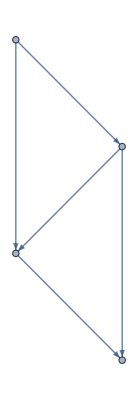

```mathematica
adj={
{∞, 5y , 81 + y, ∞},
{∞, ∞,0,13 + y},
{∞,∞,∞,6y},
{∞,∞,∞,∞}
};
MatrixForm[adj, TableHeadings->{Table[Capitalize@Alphabet[][[i]],{i,8}],Table[Capitalize@Alphabet[][[i]],{i,8}]}]
WeightedAdjacencyGraph[adj]
```

```mathematica
MatrixForm/@vardrop[adj, {30}, {{1, 4}}]
```

({1->3,3->4} | {1->2,2->4} | {1->2,2->3,3->4})

(x_2+x_3
x_1
x_3
x_2
x_1+x_3)

(5/2 (x_2+x_3)^2
81 x_1+x_1^2/2
0
13 x_2+x_2^2/2
3 (x_1+x_3)^2)

{(141.308
141.308
158.615),(x_1→8.61538
x_2→21.3846
x_3→1.2748×10^-10)}

```mathematica
EdgeList@WeightedAdjacencyGraph@adj
```

{1->2,1->3,2->3,2->4,3->4}